Alejandro Salazar Lobos	ID: 1517982
PHYS 362		Assignment #2

Q1
	The problem gives the following values for the variables:
	
		Wavelength: λ = 632 nm
		Beam area: A = 4 mm^2 = 4 · 10^-6 m^2
		Average power: P = 30 μW = 30 ·10^-6 W
		Electric field: E = E_0 sin(kx - ωt)


	(a) The power density (W/m^2) can be found from the magnitude of the Poynting vector, 
	S⃗ = ϵ_0 c^2 E⃗ x B⃗:

S⃗ = ϵ_0 c^2 (E⃗ · sin(kx - ωt)) (B⃗ · sin(kx - ωt))
|S⃗| = ϵ_0 c^2 E_0 B_0 sin^2(kx - ωt)

where ω = (2π c)/λ

Choosing the location of the specimen to be at x = 0:

|S⃗| = ϵ_0 c^2 E_0 B_0 sin^2(kx - ωt)
          = ϵ_0 c^2 E_0 B_0 (-1)^2 sin^2(ωt )
⇒ |S⃗| = ϵ_0 c^2 E_0 B_0 sin^2(ωt)

The average irradiance is I = P/A
	but 	I = ⟨|S⃗|⟩ = ϵ_0 c ⟨E_0 B_0 sin^2(ωt)⟩
      		  =  1/2 ϵ_0 c E_0^2
      		  ⇒ P/A =  1/2 ϵ_0 c E_0^2
      		  ∴ E_0 = √((2P)/(A ϵ_0 c))
      		  
      		  → |S⃗| = ϵ_0 c · (2P)/(A ϵ_0 c) sin^2(ωt)
      		  ∴  |S⃗| = (2P)/A sin^2(ωt)
 
	The following is the graph of the power density received by the specimen as a function of time from the moment the beam is turned on out to a time of 10 fs (10 · 10^-15 seconds):

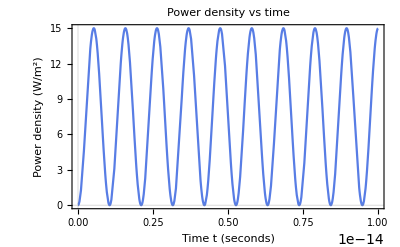

```mathematica
(* assign values to the variables *)
P = 30*10^-6; A = 4*10^-6; omega = ((3*10^8)*(2*Pi))/(632*10^-9);epsilon0= 8.85*10^-12; c = 3*10^8; E0 = ((2*P)/(A*epsilon0*c))^0.5;

(* define the function for the power density (magnitude of the Poynting vector) *)
S = (2*P/A)*(Sin[omega*t])^2; (* where t = time*)

(* plot the graph *)
Plot[S,{t,0,10*10^-15}, FrameLabel->{"Time t (seconds)", "Power density (W/m^2)"},PlotTheme->{"Scientific","BoldColor"}, PlotLabel -> "Power density vs time"]
```

(b) The time averaged Poynting vector of the sample is the irradiance, and it is the following:

I = ⟨|S⃗|⟩ = ϵ_0 c E_0^2⟨sin^2(ωt)⟩

The average of a function is given by: 1/(b-a)∫_a^b f(x)ⅆx, so

I = ϵ_0 c E_0^2 ·1/t ∫_0^t sin^2(ωs)ⅆs

(i) For Δt = 0:

I = ϵ_0 c E_0^2· lim_(t→ 0)(1/t ∫_0^t sin^2(ωs)ⅆs)= 0 // Answer

The code is as follows:

```mathematica
(* assign values to the variables *)
P = 30*10^-6; A = 4*10^-6; omega = ((3*10^8)*(2*Pi))/(632*10^-9);epsilon0= 8.85*10^-12; c = 3*10^8; E0 = ((2*P)/(A*epsilon0*c))^0.5;

(* define the integral of function to be averaged *)
int = (epsilon0*c*E0^2)*Integrate[(Sin[omega*s])^2,{s,0,t}];

(* find the limit as delta_t approaches 0 of the average of the function inside the integral (int) *)
Limit[int/t,t->0]
```

0.

(ii) For Δt = ∞:

I = ϵ_0 c E_0^2· lim_(t→ ∞)(1/t ∫_0^t sin^2(ωs)ⅆs)= 7.5 W/m^2 // Answer

The code is as follows:

```mathematica
(* assign values to the variables *)
P = 30*10^-6; A = 4*10^-6; omega = ((3*10^8)*(2*Pi))/(632*10^-9);epsilon0= 8.85*10^-12; c = 3*10^8; E0 = ((2*P)/(A*epsilon0*c))^0.5;

(* define the integral of function to be averaged *)
int = (epsilon0*c*E0^2)*Integrate[(Sin[omega*s])^2,{s,0,t}];

(* find the limit as delta_t approaches Infinity of the average of the function inside the integral (int) *)
Limit[int/t,t->Infinity]
```

7.5

(c)  To calculate the average irradiance, we have to determine the same irradiance I as a function of the change in time:

I = ⟨|S⃗|⟩ = ϵ_0 c E_0^2⟨sin^2(ωt)⟩. Using the equation for the average of a function 1/(b-a)∫_a^b f(x)ⅆx, we get:
I  = ϵ_0 c E_0^2 · 1/Δt∫_0^Δt sin^2(ω·s)ⅆs

Do the substitution ωs = u ⟹ ds = du/ω  :

I = ϵ_0 c E_0^2 · 1/(ω·Δt)∫_(u = 0)^(u = ω·Δt) sin^2(u)ⅆu

Define T ≡ ω · Δt :

I = ϵ_0 c E_0^2 · 1/T∫_0^T sin^2(u) ⅆu

Using E_0^2 = (2·P)/(A ϵ_0 c):

I = (2·P)/A· 1/T∫_0^T sin^2(u) ⅆu

The following code does the integration and graphing:

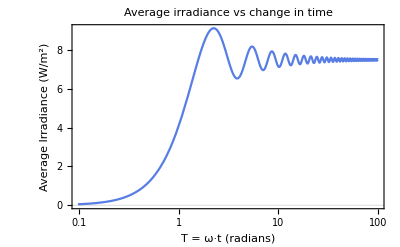

```mathematica
(* assign values to the variables *)
P = 30*10^-6; A = 4*10^-6; omega = ((3*10^8)*(2*Pi))/(632*10^-9);epsilon0= 8.85*10^-12; c = 3*10^8; E0 = ((2*P)/(A*epsilon0*c))^0.5;

(* compute the integration of the average irradiance *)

(* define the the integral of the function to be averaged *)
int = (2*P/A)*Integrate[(Sin[u])^2,{u,0,T}];

(* compute the average of the function inside the integral (int) and plot *)
LogLinearPlot[int/T,{T,0,100}, FrameLabel->{"T = ω·t (radians)", "Average Irradiance (W/m^2)"},PlotTheme->{"Scientific","BoldColor"}, PlotLabel ->"Average irradiance vs change in time"]
```